# Little Tests, One pyramidal lvl

## Start

```mathematica
(* Add to path packages *)
(* Add to path packages *)
packageDirectory=FileNameJoin[{ParentDirectory[ParentDirectory[ParentDirectory[NotebookDirectory[]]]],"1DPackage","*"}];
$Path=Join[$Path,FileNames[packageDirectory]];
```

```mathematica
<<"ReadSintel`"
<<"pyramid1d`"
<<"pyramidalStereoAll102`"

methods={"","SemiConstrained","Constrained","ConstrainedCorrelation"};
Do[
Get["pyramidalCyclope1D"<>met<>"`"]
,{met,methods}]
```

```mathematica
(* Declare path for SINTEL Data depending on user*)

baseSINTEL=Switch[$UserName,
"fieri","D:\\MastersMathematica\\Data\\Sintel",
"roys","/home/roys/datasets/SINTEL-stereo"
];
```

## Data

```mathematica
(* downscaling *)
r=2;
{ia,ib,id,io}=read[baseSINTEL,"Bamboo_1","0001",r,"clean"]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## Image sections

```mathematica
dims={412,176}
```

{412,176}

```mathematica
ims=Table[

tim=1;

nx=1+dims[[1]]*tim*i;
ny=1+dims[[2]]*tim*j;

{iaa,ibb,idd,ioo}=ImageTake[#,{ny,ny+dims[[2]]*tim},{nx,nx+dims[[1]]*tim}]&/@{ia,ib,id,io}

,{j,Range[0,0]},{i,Range[0,0]}];

max=MinMax[Flatten[ImageData[idd]]][[2]];
Print["max dv=", max]
ImageDimensions[idd]
```

max dv=38.6009

{413,177}

```mathematica
GraphicsGrid[ims[[All,All,1]],Spacings->-2]
```

-Graphics-

```mathematica
ims=Flatten[ims,1];
```

## V0 function

```mathematica
removeClosest[s_]:=Block[{n,c},(n=Nearest[s];
c=SortBy[Table[{i,Norm[s[[i]]-n[s[[i]],2][[2]]]},{i,1,Length[s]}],(#[[2]])&][[1,1]];
Delete[s,c])];
removeClosest[s_]:=s/;Length[s]<2;
```

## More in depth

```mathematica
ImageDimensions[idd]
```

{413,177}

```mathematica
lvl=1;
```

```mathematica
k=100;
{ka,kd}=ImageData[#][[k]]&/@{iaa,idd};
pyra=pyrFuncGen[ka,lvl];

kb=Table[pyra[[1,1]][x+kd[[x]]],{x,1,1+dims[[1]]*tim}];

pyrb=pyrFuncGen[kb,lvl];


pyrab=Flatten[{pyra, pyrb},{{2},{1},{3}}];
```

```mathematica
(* Test values *)
testLevels={{1,1}};
e=0.0001;
n=0;
u=0;
steps=1;
```

```mathematica
(* Creating list of initial Values *)
range={-10,0};
listv0=Select[RandomReal[range,{1000,2}],(Sign[#[[1]]*#[[2]]]≥0 &&Abs[#[[1]]+#[[2]]]≤ Max[Abs[range]])&];
listv0=Nest[removeClosest,listv0,Length[listv0]-80];
ListPlot[listv0];
```

```mathematica
(* Creating condition *)
topbot={-10,0};
Clear[condition];
condition[x_]:=x[[1]]*x[[2]]>0 && topbot[[1]]<Total[x[[1;;2]]]<topbot[[2]];
```

```mathematica
(* Selection criteria values *)
scale=topbot;
affiche[{p_,v_},y_]:={RainbowColor[Rescale[v,scale,{0,1}]],Point[{p-0.5,y+0.5}]};
RainbowColor[z_]:=Blend[{Purple,Blue,Cyan,Green,Yellow,Orange,Red},z];
legendBar=BarLegend[{RainbowColor,{0,1}},Ticks->Table[{i,Rescale[i,{0,1},scale]},{i,Range[0,1,0.2]}],LegendMarkerSize->100];
```

```mathematica
lt=lineTest[n,u,listv0,condition,Range[1,dims[[1]]],pyrab[[1;;1]],e,"ConstrainedCorrelation"];
```

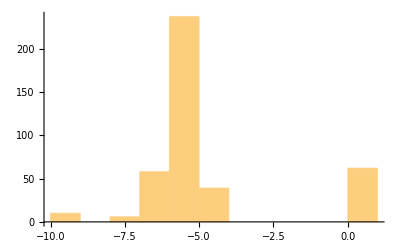

```mathematica
Histogram[Total[#]&/@lt[[All,1;;2]]]
```

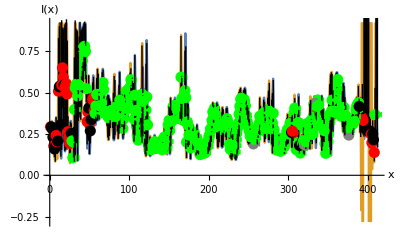

```mathematica
seeAllLine[n,u,listv0,condition,Range[1,dims[[1]]*tim],pyrab[[1;;1]],e,"ConstrainedCorrelation"]
```

```mathematica
(*pixelIterGraphics[10,1,0,20,{{0.,0.}},condition,5, 1,pyrab[[1;;1]],e,"ConstrainedCorrelation"]*)
```

## Little functions

```mathematica
(*[steps,n,u,listv0,condition,e,{levels},ims]*)
bigTest[steps_,n_,u_,listv0_,condition_,e_,minmaxList_,imslist_]:=Block[{ic,depth, resTable,realPVTable,okTable,realOkPVTable,pos,pv,g0,nonresTable,nonrealPVTable},(
Table[
Table[
depth=stereoDepth[n,u,listv0,condition,im[[1]],im[[2]],im[[3]],minmax[[2]],minmax,Range[1,1+dims[[1]]*tim,steps],Range[1,1+dims[[2]]*tim],e,"ConstrainedCorrelation"];

(* We only keep converged solutions *)
resTable=Table[
Select[depth[[r]],#[[2]]=="converged"&]
(*depth[[r]]*)
,{r,1+dims[[2]]*tim}];

(* We give right coordinates to each solution *)
realPVTable=Table[
pos=resTable[[r,All,5]]-resTable[[r,All,3]];
pv=Thread[{pos,resTable[[r,All,1]]}]
,{r,1+dims[[2]]*tim}];

(* We only keep ok solutions *)
okTable=Table[
Select[depth[[r]],#[[2]]=="ok"&]
(*depth[[r]]*)
,{r,1+dims[[2]]*tim}];

(* We give right coordinates to each solution *)
realOkPVTable=Table[
pos=okTable[[r,All,5]]-okTable[[r,All,3]];
pv=Thread[{pos,okTable[[r,All,1]]}]
,{r,1+dims[[2]]*tim}];

(* We only keep NON converged solutions *)
nonresTable=Table[
Select[depth[[r]],(#[[2]]!="converged"&&#[[2]]!="ok")&]
(*depth[[r]]*)
,{r,1+dims[[2]]*tim}];

(* We give right coordinates to each solution *)
nonrealPVTable=Table[
pos=nonresTable[[r,All,5]]-nonresTable[[r,All,3]];
pv=Thread[{pos,nonresTable[[r,All,1]]}]
,{r,1+dims[[2]]*tim}];

(* We create g0 *)
g0=Graphics[{PointSize[0.003],Table[affiche[#,1+dims[[2]]*tim-y]&/@realPVTable[[y]],{y,1,1+dims[[2]]*tim}]}];
g0=Rasterize[Show[im[[1]],g0],ImageSize->ImageDimensions[im[[1]]]*5,ImageResolution->300];

{realPVTable,realOkPVTable,nonrealPVTable,g0}

,{minmax,minmaxList}]
,{im, imslist}]
)]
```

## Big Tests

### Test Run

```mathematica
Print["minmax dv=",MinMax[Flatten[ImageData[id]]]]
```

minmax dv={0.136895,38.6009}

```mathematica
(* Test values *)
levels={{1,1}};
e=0.0001;
n=0;
u=0;
steps=1;
```

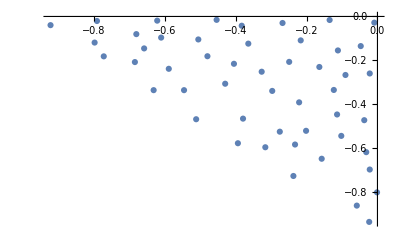

```mathematica
(* Creating list of initial Values *)
range={-10*0.1,0};
listv0=Select[RandomReal[range,{3000,2}],(Sign[#[[1]]*#[[2]]]≥0 &&Abs[#[[1]]+#[[2]]]≤ Max[Abs[range]])&];
listv0=Nest[removeClosest,listv0,Length[listv0]-50];
ListPlot[listv0]
```

```mathematica
(* Creating condition *)
topbot={-10*0.1,0};
Clear[condition];
condition[x_]:=x[[1]]*x[[2]]>0 && topbot[[1]]<Total[x[[1;;2]]]<topbot[[2]];
```

```mathematica
(* Selection criteria values *)
scale=topbot;
affiche[{p_,v_},y_]:={RainbowColor[Rescale[v,scale,{0,1}]],Point[{p-0.5,y+0.5}]};
RainbowColor[z_]:=Blend[{Purple,Blue,Cyan,Green,Yellow,Orange,Red},z];
legendBar=BarLegend[{RainbowColor,{0,1}},Ticks->Table[{i,Rescale[i,{0,1},scale]},{i,Range[0,1,0.2]}]];
```

```mathematica
solution = bigTest[steps,n,u,listv0,condition,e,levels,ims];
```

{10,20}

{20,20}

{30,20}

{40,20}

{50,20}

{60,20}

{70,20}

{80,20}

{90,20}

{100,20}

{110,20}

{120,20}

{130,20}

{140,20}

{150,20}

{160,20}

{170,20}

{180,20}

{190,20}

{200,20}

{210,20}

{10,30}

{220,20}

{20,30}

{30,30}

{40,30}

{230,20}

{50,30}

{60,30}

{240,20}

{70,30}

{80,30}

{250,20}

{90,30}

{260,20}

{100,30}

{110,30}

{270,20}

{280,20}

{120,30}

{290,20}

{130,30}

{300,20}

{310,20}

{140,30}

{320,20}

{150,30}

{330,20}

{160,30}

{340,20}

{10,10}

{170,30}

{10,60}

{20,10}

{350,20}

{20,60}

{30,10}

{30,60}

{40,10}

{180,30}

{40,60}

{50,10}

{50,60}

{360,20}

{60,10}

{60,60}

{70,10}

{190,30}

{70,60}

{80,10}

{10,50}

{80,60}

{90,10}

{200,30}

{20,50}

{370,20}

{90,60}

{100,10}

{30,50}

{100,60}

{110,10}

{40,50}

{110,60}

{210,30}

{50,50}

{380,20}

{60,50}

{120,10}

{120,60}

{70,50}

{10,40}

{220,30}

{80,50}

{20,40}

{90,50}

{30,40}

{130,60}

{130,10}

{390,20}

{40,40}

{100,50}

{140,60}

{50,40}

{230,30}

{60,40}

{140,10}

{110,50}

{70,40}

{150,60}

{400,20}

{80,40}

{240,30}

{150,10}

{120,50}

{160,60}

{90,40}

{130,50}

{410,20}

{160,10}

{250,30}

{170,60}

{140,50}

{170,10}

{100,40}

{180,10}

{260,30}

{180,60}

{110,40}

{150,50}

{120,40}

{190,10}

{270,30}

{190,60}

{130,40}

{160,50}

{200,10}

{280,30}

{140,40}

{170,50}

{210,10}

{200,60}

{290,30}

{220,10}

{150,40}

{180,50}

{210,60}

{300,30}

{230,10}

{160,40}

{190,50}

{220,60}

{240,10}

{310,30}

{170,40}

{200,50}

{230,60}

{250,10}

{210,50}

{320,30}

{180,40}

{240,60}

{260,10}

{330,30}

{190,40}

{220,50}

{250,60}

{200,40}

{270,10}

{230,50}

{340,30}

{260,60}

{280,10}

{210,40}

{240,50}

{350,30}

{270,60}

{290,10}

{220,40}

{300,10}

{250,50}

{360,30}

{280,60}

{310,10}

{230,40}

{260,50}

{320,10}

{370,30}

{290,60}

{240,40}

{330,10}

{270,50}

{380,30}

{300,60}

{340,10}

{280,50}

{250,40}

{390,30}

{350,10}

{290,50}

{260,40}

{310,60}

{400,30}

{320,60}

{300,50}

{410,30}

{360,10}

{270,40}

{330,60}

{310,50}

{370,10}

{280,40}

{340,60}

{320,50}

{380,10}

{350,60}

{290,40}

{330,50}

{360,60}

{390,10}

{300,40}

{340,50}

{370,60}

{400,10}

{310,40}

{350,50}

{380,60}

{410,10}

{360,50}

{320,40}

{390,60}

{330,40}

{370,50}

{400,60}

{410,60}

{380,50}

{340,40}

{390,50}

{350,40}

{360,40}

{400,50}

{370,40}

{410,50}

{380,40}

{390,40}

{400,40}

{410,40}

{10,70}

{20,70}

{30,70}

{40,70}

{50,70}

{60,70}

{70,70}

{80,70}

{90,70}

{100,70}

{110,70}

{120,70}

{130,70}

{140,70}

{150,70}

{160,70}

{170,70}

{180,70}

{190,70}

{200,70}

{210,70}

{220,70}

{230,70}

{240,70}

{250,70}

{260,70}

{270,70}

{280,70}

{290,70}

{300,70}

{310,70}

{320,70}

{330,70}

{340,70}

{350,70}

{360,70}

{370,70}

{380,70}

{390,70}

{400,70}

{410,70}

{10,120}

{20,120}

{30,120}

{10,80}

{40,120}

{20,80}

{30,80}

{50,120}

{40,80}

{50,80}

{60,80}

{60,120}

{70,80}

{80,80}

{70,120}

{90,80}

{80,120}

{100,80}

{110,80}

{90,120}

{120,80}

{100,120}

{130,80}

{110,120}

{140,80}

{120,120}

{150,80}

{130,120}

{160,80}

{140,120}

{170,80}

{150,120}

{180,80}

{160,120}

{10,110}

{20,110}

{190,80}

{170,120}

{30,110}

{200,80}

{40,110}

{180,120}

{10,90}

{50,110}

{210,80}

{20,90}

{190,120}

{30,90}

{40,90}

{60,110}

{220,80}

{200,120}

{50,90}

{60,90}

{70,110}

{230,80}

{70,90}

{210,120}

{80,90}

{80,110}

{90,90}

{240,80}

{220,120}

{100,90}

{250,80}

{90,110}

{230,120}

{110,90}

{260,80}

{100,110}

{240,120}

{120,90}

{270,80}

{110,110}

{250,120}

{130,90}

{10,100}

{20,100}

{280,80}

{260,120}

{30,100}

{120,110}

{140,90}

{40,100}

{270,120}

{290,80}

{50,100}

{60,100}

{130,110}

{150,90}

{280,120}

{300,80}

{290,120}

{70,100}

{160,90}

{140,110}

{300,120}

{310,80}

{80,100}

{170,90}

{310,120}

{150,110}

{320,80}

{320,120}

{180,90}

{160,110}

{90,100}

{330,80}

{330,120}

{190,90}

{340,120}

{170,110}

{100,100}

{350,120}

{340,80}

{360,120}

{200,90}

{370,120}

{110,100}

{180,110}

{380,120}

{350,80}

{210,90}

{390,120}

{400,120}

{120,100}

{220,90}

{190,110}

{410,120}

{360,80}

{130,100}

{200,110}

{230,90}

{370,80}

{140,100}

{210,110}

{240,90}

{380,80}

{150,100}

{390,80}

{220,110}

{250,90}

{160,100}

{400,80}

{230,110}

{260,90}

{170,100}

{410,80}

{240,110}

{270,90}

{180,100}

{250,110}

{190,100}

{280,90}

{260,110}

{200,100}

{290,90}

{270,110}

{210,100}

{300,90}

{280,110}

{220,100}

{310,90}

{290,110}

{320,90}

{230,100}

{300,110}

{330,90}

{240,100}

{310,110}

{340,90}

{320,110}

{250,100}

{330,110}

{350,90}

{260,100}

{340,110}

{360,90}

{350,110}

{270,100}

{370,90}

{360,110}

{370,110}

{280,100}

{380,110}

{380,90}

{390,110}

{400,110}

{290,100}

{390,90}

{410,110}

{300,100}

{400,90}

{310,100}

{410,90}

{320,100}

{10,160}

{20,160}

{330,100}

{30,160}

{340,100}

{40,160}

{350,100}

{50,160}

{360,100}

{60,160}

{370,100}

{70,160}

{380,100}

{80,160}

{390,100}

{400,100}

{90,160}

{410,100}

{100,160}

{110,160}

{120,160}

{130,160}

{140,160}

{150,160}

{160,160}

{170,160}

{180,160}

{190,160}

{200,160}

{210,160}

{220,160}

{230,160}

{240,160}

{250,160}

{260,160}

{270,160}

{280,160}

{290,160}

{300,160}

{310,160}

{320,160}

{330,160}

{340,160}

{350,160}

{360,160}

{370,160}

{380,160}

{390,160}

{400,160}

{410,160}

{10,170}

{20,170}

{30,170}

{40,170}

{50,170}

{60,170}

{70,170}

{80,170}

{90,170}

{100,170}

{110,170}

{120,170}

{130,170}

{140,170}

{150,170}

{160,170}

{170,170}

{180,170}

{190,170}

{200,170}

{210,170}

{220,170}

{230,170}

{240,170}

{250,170}

{260,170}

{270,170}

{280,170}

{290,170}

{300,170}

{310,170}

{320,170}

{330,170}

{340,170}

{350,170}

{360,170}

{370,170}

{380,170}

{390,170}

{400,170}

{410,170}

{10,130}

{20,130}

{30,130}

{40,130}

{50,130}

{60,130}

{70,130}

{80,130}

{90,130}

{100,130}

{110,130}

{120,130}

{130,130}

{140,130}

{150,130}

{160,130}

{170,130}

{180,130}

{190,130}

{200,130}

{210,130}

{220,130}

{230,130}

{240,130}

{250,130}

{260,130}

{270,130}

{280,130}

{290,130}

{300,130}

{310,130}

{320,130}

{330,130}

{340,130}

{350,130}

{360,130}

{370,130}

{380,130}

{390,130}

{400,130}

{410,130}

{10,140}

{20,140}

{30,140}

{40,140}

{50,140}

{60,140}

{10,150}

{70,140}

{20,150}

{80,140}

{30,150}

{90,140}

{40,150}

{50,150}

{100,140}

{60,150}

{110,140}

{120,140}

{70,150}

{130,140}

{80,150}

{90,150}

{140,140}

{150,140}

{100,150}

{110,150}

{160,140}

{170,140}

{120,150}

{180,140}

{130,150}

{190,140}

{140,150}

{150,150}

{200,140}

{160,150}

{210,140}

{170,150}

{220,140}

{180,150}

{230,140}

{190,150}

{240,140}

{200,150}

{250,140}

{210,150}

{260,140}

{220,150}

{270,140}

{280,140}

{230,150}

{290,140}

{240,150}

{300,140}

{310,140}

{250,150}

{320,140}

{260,150}

{330,140}

{340,140}

{350,140}

{360,140}

{270,150}

{370,140}

{380,140}

{390,140}

{280,150}

{400,140}

{410,140}

{290,150}

{300,150}

{310,150}

{320,150}

{330,150}

{340,150}

{350,150}

{360,150}

{370,150}

{380,150}

{390,150}

{400,150}

{410,150}

```mathematica
Print["levelTable Dimensions=",Dimensions[solution]]
```

levelTable Dimensions={1,1,4}

```mathematica
solution[[1,1,1,6]];
```

### Images

```mathematica
Dimensions[ims]
```

{1,4}

```mathematica
imagesTable=Table[

groundTruth=Image[Table[Map[RainbowColor,imd],{imd,ImageData[Rescale[-ims[[which,3]]*0.1,scale,{0,1}]]}]];

ConformImages[Rasterize[Image[#],ImageResolution->200]&/@Flatten[{solution[[which,1,4]],groundTruth}],{900}]


,{which,Length[ims]}];
```

```mathematica
im1=GraphicsGrid[Partition[imagesTable[[All,1]],1],Spacings->-2];
im2=GraphicsGrid[Partition[imagesTable[[All,2]],1],Spacings->-2];
```

```mathematica
legendBar=BarLegend[{RainbowColor,{0,1}},Ticks->Table[{i,Rescale[i,{0,1},scale]},{i,Range[0,1,0.2]}],LegendMarkerSize->100];
```

```mathematica
imFinal=Legended[GraphicsRow[{im1,im2},ImageSize->Large,Spacings->-25],legendBar]
```

-Graphics-

```mathematica
nbname=StringDelete[Last@FileNameSplit@NotebookFileName[],".nb"];
```

```mathematica
figsDirectory=FileNameJoin[{ParentDirectory[NotebookDirectory[]],"fullSintelDataset"}];

Export[FileNameJoin[{figsDirectory,nbname<>"-im.pdf"}],Rasterize[imFinal,ImageSize->500,ImageResolution->200]]
```

D:\MastersMathematica\Matematica\MathematicaOpticalFlow\CyclopeanOpticalFlow\Figures\figs\fullSintelDataset\sintel-bamboo102-clean-Full-im.pdf

### More numbers

```mathematica
fontsize=16;
```

```mathematica
numbersTable=Table[

groundTruth=ImageData[-ims[[which,3]]*0.1];
solution[[which,1,1]];

density=(Length[Flatten[DeleteDuplicates[#]&/@Floor[solution[[which,1,1,All,All,1]]]]])/((1.+dims[[1]]*tim)*(1.+dims[[2]]*tim));

vals=Table[
ps=Select[solution[[which,1,1,y,All,All]],1<Round[#[[1]]]<(1.+dims[[1]]*tim)&];
(ps[[All,2]]-groundTruth[[y,Round[ps[[All,1]]]]])^2

,{y,Length[solution[[which,1,1]]]}];

rmse=Sqrt[Mean[Flatten[vals]]];

{Style["RMSE= ",FontSize->fontsize,FontFamily->"Times",Italic],rmse,Style["Density= ",FontSize->fontsize,FontFamily->"Times",Italic],density}

,{which,Length[ims]}]
```

{{RMSE= ,0.179039,Density= ,0.546244}}

### Histogram

```mathematica
fontsize=30;
imagesize=500;
maxvalue={{-1.2,0.1},{0,10000}};
```

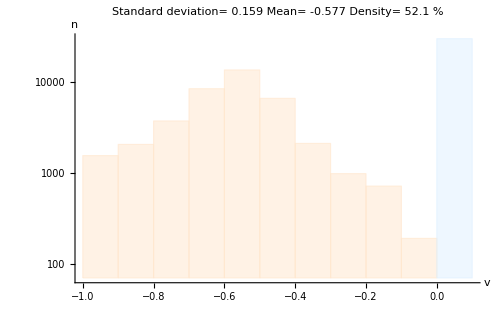

```mathematica
histogramGrid=
Table[

convergedData=Flatten[solution[[idxims,1,1,All,All,2]]];
okData=Flatten[solution[[idxims,1,2,All,All,2]]];
nonConvergedData=Flatten[solution[[idxims,1,3,All,All,2]]];

std=StandardDeviation[convergedData];
mu=Mean[convergedData];
density=((Length[Flatten[DeleteDuplicates[#]&/@Round[solution[[idxims,1,1,All,All,1]]]]])/((1.+dims[[1]]*tim)*(1.+dims[[2]]*tim)))*100;

Histogram[{convergedData, nonConvergedData},10,"LogCount",
PlotLabel->Column[{
Style[Row[{"Standard deviation= ",NumberForm[std,3]}],FontSize->fontsize,FontFamily->"Times",Italic],
Style[Row[{"Mean= ",NumberForm[mu,3]}],FontSize->fontsize, FontFamily->"Times",Italic],
Style[Row[{"Density= ",NumberForm[density,3]," %"}],FontSize->fontsize, FontFamily->"Times",Italic]},
Spacings->0.1,
Alignment->Center],
PlotRange->maxvalue,
ImageSize->imagesize,
AxesLabel->{Style["v",FontSize->fontsize,FontFamily->"Times",Italic],Style["n",FontSize->fontsize,FontFamily->"Times",Italic]},ChartStyle->{LightOrange,LightBlue,LightGreen},TicksStyle->fontsize-6]
,{idxims,Length[ims]}]
```

```mathematica
dims[[1]]*dims[[2]];
Dimensions[convergedData];
```

```mathematica
convergedData=Select[Flatten[ImageData[-ims[[1,3]]*0.1]], topbot[[1]]<#<topbot[[2]]&];

std=StandardDeviation[convergedData];
mu=Mean[convergedData];
density=(Dimensions[convergedData][[1]]/(dims[[1]]*dims[[2]]))*100.;
```

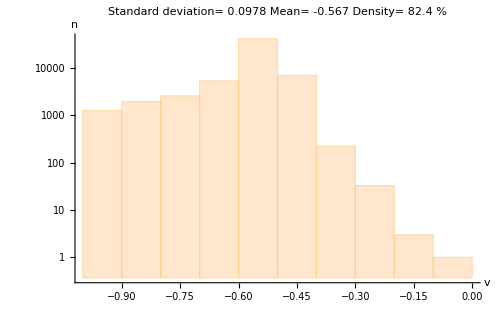

```mathematica
hGroundTruth=Histogram[convergedData,10,"LogCount",
PlotLabel->Column[{
Style[Row[{"Standard deviation= ",NumberForm[std,3]}],FontSize->fontsize,FontFamily->"Times",Italic],
Style[Row[{"Mean= ",NumberForm[mu,3]}],FontSize->fontsize, FontFamily->"Times",Italic],
Style[Row[{"Density= ",NumberForm[density,3]," %"}],FontSize->fontsize, FontFamily->"Times",Italic]},
Spacings->0.1,
Alignment->Center],
PlotRange->maxvalue,
ImageSize->imagesize,
AxesLabel->{Style["v",FontSize->fontsize,FontFamily->"Times",Italic],Style["n",FontSize->fontsize,FontFamily->"Times",Italic]},
ChartStyle->{LightOrange},TicksStyle->fontsize-6]
```

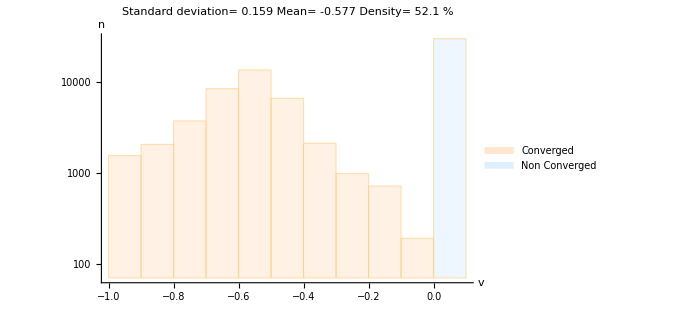
-Graphics--Graphics-

```mathematica
hFinal=Legended[
Row[{histogramGrid[[1]],hGroundTruth}],
Placed[SwatchLegend[{LightOrange, LightBlue, LightGreen},{Style["Converged",FontSize->fontsize, FontFamily->"Times",Italic], Style["Non Converged",FontSize->fontsize, FontFamily->"Times",Italic]},LegendLayout->"Row"],Below]]
```

```mathematica
figsDirectory=FileNameJoin[{ParentDirectory[NotebookDirectory[]],"fullSintelDataset"}];

Export[FileNameJoin[{figsDirectory,nbname<>"-his.pdf"}],Rasterize[hFinal,ImageSize->500,ImageResolution->200]]
```

D:\MastersMathematica\Matematica\MathematicaOpticalFlow\CyclopeanOpticalFlow\Figures\figs\fullSintelDataset\sintel-bamboo102-clean-Full-his.pdf